```mathematica
(* Radiative Quenching, Chapter 3 *)
(* This one uses my paper *)

(* Upper Limit for integration *)
limit = 20;

(*electron mass *)
Subscript[m, e]=1;
(* Proton Mass *)
Subscript[m, p]=1836;
(* Reduced Mass *)
μ=Subscript[m, p]/2;
hbar= 1;  
c=137 ;(*SpeedOfLight, atomic units*)
 
vSg1RawData = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg1.mx"];
vSg2RawData = Import["~/Work/Physics-Thesis/thesis-2/MathematicaCode/sg2.mx"];
(* Extrapolate to R = 40 *)
vSg1Data=Table[{vSg1RawData[[i]][[1]],vSg1RawData[[i]][[5]]},{i,1,Length[vSg1RawData]}];
vSg2Data=Table[{vSg2RawData[[i]][[1]],vSg2RawData[[i]][[5]]},{i,1,Length[vSg2RawData]}];

vSg1Data=Join[vSg1Data,Table[{i,vSg1Data[[Length[vSg1Data]]][[2]]},{i,11,40,1}]];
vSg2Data=Join[vSg2Data,Table[{i,vSg2Data[[Length[vSg2Data]]][[2]]},{i,11,40,1}]];

(* Load Potential curves for 1sg, 2sg states 
"R","p", "A","E","E+1/r"*)
(* 1sg state, potential curve *)
Subscript[v, a]=Interpolation[Transpose[{vSg1Data[[All,1]],vSg1Data[[All,2]]}], InterpolationOrder->3];
(* 2sg state, potential curve *)
Subscript[v, b]=Interpolation[Transpose[{vSg2Data[[All,1]],vSg2Data[[All,2]]}], InterpolationOrder->3];

deltaV[r_]:=Abs[Subscript[v, a][r]-Subscript[v, b][r]];

(*Plot[{Subscript[v, a][r],Subscript[v, b][r]},{r,0,40}]*)
```

```mathematica
(* calculate Transition dipole moment *)
(* Subscript[ψ, a](r)=f, Subscript[ψ, b](r)=g *)
solA[r_]:= Sort[Transpose[NDEigensystem[-1/(2 Subscript[m, e])f''[x]+Subscript[v, a][r]f[x],f[x],{x,0.1,limit},All,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}] ]] [[1]][[2]];

solB[r_]:=Sort[Transpose[NDEigensystem[-1/(2 Subscript[m, e])g''[x]+Subscript[v, b][r]g[x],g[x],{x,0.1,limit},All,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}] ]] [[1]][[2]];



(* Norm comes as 1 from the NDEigensystem *)
(*Subscript[norm, A][r_]:=NIntegrate[solA[r]solA[r],{x,0.1,limit}] ;
Subscript[norm, B][r_]:=NIntegrate[solB[r]solB[r],{x,0.1,limit}] ;*)
```

```mathematica
(* radial transition dipole moment d(r)= <Subscript[ψ, a]^*(r) r Subscript[ψ, b](r)> *)

fTemp[r_ ]:=  Conjugate[solA[r]] * r * solB[r];

d[r_]:=Map[NIntegrate[# , {x,.1, limit}] & ,fTemp[r]];

(* Calculate A(R)*)
a[r_]:=4/3(d[r])^2(deltaV[r])^3/c^3 ;
(*Subscript[norm, A][1]
Subscript[norm, B][1]*)
d[1]
a[1]
Subscript[v, a][1]
Subscript[v, b][1]
```

19.9

0.00504494

-2.5469

0.360187

```mathematica
solNear=Sort[Transpose[NDEigensystem[-1/(2μ)ff''[x]+(Subscript[v, a][x]-I/2 a[x])ff[x],ff,{x,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];

solFar=Sort[Transpose[NDEigensystem[-1/(2μ)ff''[x]+Subscript[v, b][x]ff[x],ff,{x,0.2, limit}, 5,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}]]];

(* k = √(2 mE/ℏ)*)
Print["E far=",solFar[[1]][[1]]]
Print["E near=", solNear[[1]][[1]]]

kF =(√(2 Subscript[m, p] Abs[solFar[[1]][[1]]]))/hbar;
kN =(√(2 Subscript[m, p] solNear[[1]][[1]]))/hbar;
fNear=solNear[[1]][[2]];
fFar = solFar[[1]][[2]];
Print["K far=",kF, ", ", Abs[kF]]
Print["K near=", kN, ", ",Abs[kN]]
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«1»,«1»,{1,{{«1»},{«1»}},{0.000133333+0. ⅈ,-0.0000333333+0. ⅈ,0.0000666667+0. ⅈ,-0.0000333333+0. ⅈ,0.000266667+0. ⅈ,«158392»,0.000533333+0. ⅈ,0.0000666667+0. ⅈ,0.0000666667+0. ⅈ,0.000533333+0. ⅈ}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

E far=-0.00919919

E near=-1.29058-3.23615 ⅈ

K far=5.81201, 5.81201

K near=63.4596-93.6277 ⅈ, 113.107

kF=5.81201

kN=63.4596-93.6277 ⅈ ,Abs[kN]=113.107

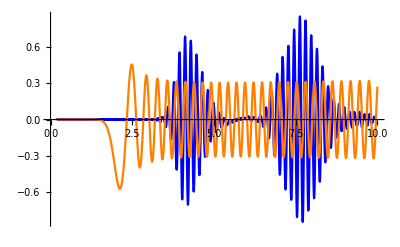

0.0978251

-0.209337

```mathematica
(* Now to calculate the phase shift we match the Subscript[f, R] in the region V = 0 with the solution in V = 0 , which is represented by the Bessel Functions. *)
(* We use logarithmic derivative *)
Print["kF=",kF]
Print["kN=",kN," ,Abs[kN]=",Abs[kN]]
fFar2[k_,r_]:=BesselJ[0, kF r] + BesselY[0,kF r];

Plot[{Im[fNear[ r]], fFar[r], Sqrt[2/(Pi kF r)] BesselJ[0, kN r]},{r,0,10}, PlotStyle->{Blue,Orange, Red}]


Abs[fNear[9]]
fFar[9]
logBeta[x_] := fNear'[x]/fNear[x];
```

```mathematica
(* For far away region *)
(* S wave *)
(* Derive a Bessel function at a point *)
fD[f_,l_,r_]:=N[D[f[l,x],x]/. x->r];
fD[BesselJ,0,0.13642084936916368-0.3992724676792502I]


tanPhase1[k_,r_]:=(k r fD[BesselJ,0,k r]-logBeta[r]N[BesselJ[0,k r]])/(k r fD[BesselY,0,k r]-logBeta[r]N[BesselY[0,k  r]]);
tanPhase2[k_,r_]:=(k r Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k r Sin[k  r]);

tanPhase3[k_,r_]:=(k Cos[k r]-logBeta[r]Sin[k r])/(logBeta[r]Cos[k r]+k  Sin[k  r]);

kS
Table[{r,tanPhase1[kS,r]},{r,5,limit,1}] //MatrixForm
Table[{r,tanPhase2[kS,r]},{r,5,limit,1}] //MatrixForm
Table[{r,tanPhase3[kS,r]},{r,5 ,limit,1}] //MatrixForm
```

-0.0721643+0.202218 ⅈ

-0.0060197-0.00173882 ⅈ

(5 | -0.267686+0.214983 ⅈ
6 | -0.270433+0.229083 ⅈ
7 | -0.271964+0.244309 ⅈ
8 | -0.27284+0.248951 ⅈ
9 | -0.272143+0.270628 ⅈ
10 | -0.273853+0.276724 ⅈ
11 | -0.273406+0.287084 ⅈ
12 | -0.27267+0.296788 ⅈ
13 | -0.271574+0.30628 ⅈ
14 | -0.270088+0.315739 ⅈ
15 | -0.26812+0.325439 ⅈ
16 | -0.265443+0.33588 ⅈ
17 | -0.261449+0.348173 ⅈ
18 | -0.254077+0.365577 ⅈ
19 | -0.230336+0.40384 ⅈ
20 | -0.0105984-0.00619644 ⅈ)

(5 | 0.0304986+0.00866435 ⅈ
6 | 0.0367097+0.0104381 ⅈ
7 | 0.0442285+0.0122797 ⅈ
8 | 0.0466845+0.0131675 ⅈ
9 | 0.059431+0.0156786 ⅈ
10 | 0.0632307+0.017795 ⅈ
11 | 0.070263+0.0196814 ⅈ
12 | 0.077301+0.0215965 ⅈ
13 | 0.0846328+0.0235621 ⅈ
14 | 0.0924001+0.0256002 ⅈ
15 | 0.100859+0.0277504 ⅈ
16 | 0.110521+0.0300919 ⅈ
17 | 0.12258+0.0328099 ⅈ
18 | 0.14063+0.0364653 ⅈ
19 | 0.182744+0.0439333 ⅈ
20 | -7.61529+2.21387 ⅈ)

(5 | 0.030184+0.00869429 ⅈ
6 | 0.0362266+0.0104448 ⅈ
7 | 0.0424525+0.0122052 ⅈ
8 | 0.0479979+0.0138452 ⅈ
9 | 0.0547962+0.0156924 ⅈ
10 | 0.0605494+0.0174841 ⅈ
11 | 0.0666504+0.0192517 ⅈ
12 | 0.0727447+0.021024 ⅈ
13 | 0.078857+0.0228029 ⅈ
14 | 0.0849947+0.0245898 ⅈ
15 | 0.091171+0.0263871 ⅈ
16 | 0.0974115+0.0281989 ⅈ
17 | 0.103776+0.0300348 ⅈ
18 | 0.110443+0.0319222 ⅈ
19 | 0.118304+0.033997 ⅈ
20 | -7.40941+1.99344 ⅈ)